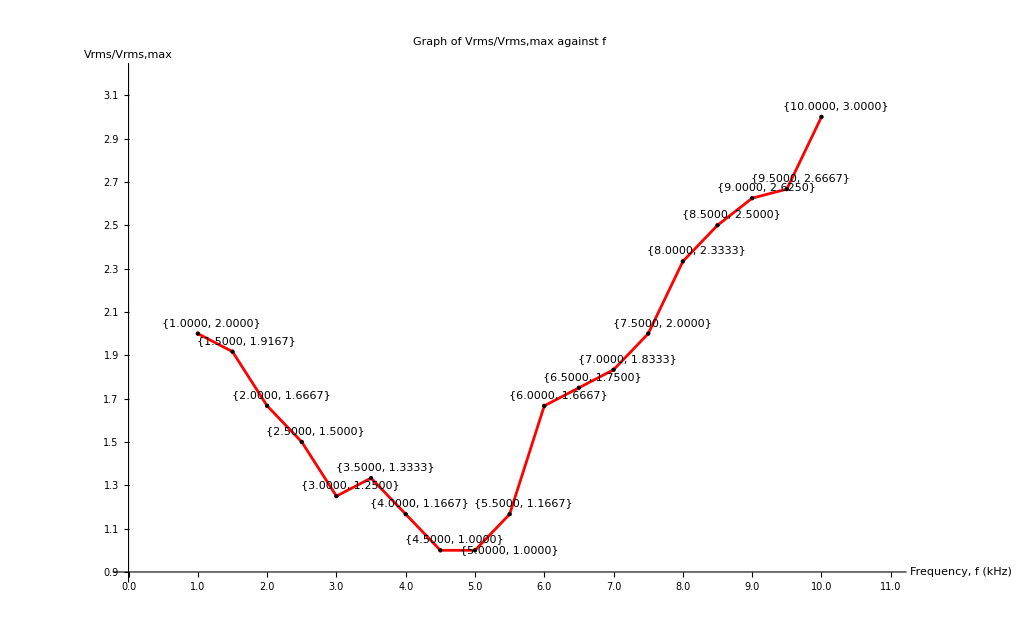

```mathematica
data={{1.0,2.0000},{1.5,1.9167},{2.0,1.6667},{2.5,1.5000},{3.0,1.2500},{3.5,1.3333},{4.0,1.1667},{4.5,1.0000},{5.0,1.0000},{5.5,1.1667},{6.0,1.6667},{6.5,1.7500},{7.0,1.8333},{7.5,2.0000},{8.0,2.3333},{8.5,2.5000},{9.0,2.6250},{9.5,2.6667},{10.0,3.0000}};

ListLinePlot[data,PlotStyle->Red,Mesh->All,MeshStyle->PointSize[Medium],AxesLabel->{"Frequency, f (kHz)","Vrms/Vrms,max"},PlotLabel->"Graph of Vrms/Vrms,max against f",Epilog->{Point[data],Text[Style[ToString@NumberForm[#,{5,4}],Black],#+{0.2,0.05}]&/@Select[data,#[[1]]!=5.0&],Text[Style[ToString@NumberForm[data[[9]],{4,4}],Black],data[[9]]+{0.5,0}]  (*Label for {5.0,1.0000}*)},PlotRange->{{0,11.0},{0.9,3.2}},Ticks->{{#,NumberForm[#,{3,1}]}&/@Range[0,11.0,0.5],{#,NumberForm[#,{3,1}]}&/@Range[0.9,3.2,0.1]}]
```